# Arnoldi Iteration (Cont)

How and why does the Arnoldi eigenvalue work? We have a lot of slightly fancy machinery.  We construct and are looking in the Krylov space
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
By definition any x∈𝒦_n(A,b)  satisfies x=c_0 b+c_1 A.b+ c_2 A^2.b+…+c_(n-1)A^(n-1).b=q(A).b where q(A) is the polynomial
	q(A)=c_0 Id+c_1 A+ c_2 A^2+…+c_(n-1)A^(n-1).
The question is what do we gain by writing/thinking of this as in terms of matrix polynomials!

We will see that the polynomial implicitly built by Arnoldi and other Krylov methods is the best polynomial in a very specific sense which gives convergence information.

## Polynomial Lemniscate: https://en.wikipedia.org/wiki/Polynomial_lemniscate

A lemniscate of a polynomial p(z) is a level set of |p(z)|=c.  You can plot these. They can be complicated.

```mathematica
p[z_]:=8.9-4 z-3 z^2+6 z^3-7 z^4+2 z^6+9 z^7+6 z^8-2 z^9
ContourPlot[ Abs[p[x+ I y]], {x, -1.5,1},{y,-1.2,1.2},
ContourLabels->All,
PlotPoints->100,
Epilog->{Red, Point[ReIm[NSolveValues[p[z]==0,z]]]},
Contours->{1,2,3,4,5,6,7,8,9,10}]
```

-Graphics-

You can see the zeros sitting in the middle of each blob.  Once the contours are small enough the blobs separate. Eventually if the roots are isolated each root is in one blob!

## Arnoldi Reminder

Just as a reminder: The Arnoldi process iteratively computes a nested sequence of orthogonal matrices Q_n∈ℝ^(m×n) and rectangular Upper Hessenberg matrices H_n∈ℝ^((n+1)×n).  Columns of Q_n are an orthonormal basis for the Krylov space	
	𝒦_n(A,b):=span({b,A.b,A^2.b,…,A^(n-1).b}).
By construction, A maps 𝒦_n(A,b)→𝒦_(n+1)(A,b) with H_n the matrix for this map in the orthogonal basis. In other words, since H_n is Upper Hessenberg
	A.Q_n=Q_(n+1).H_n=Q_n.H_n[1:n,1:n]+H_n[n+1,n] q_(n+1). 
If the bottom corner of H_n is zero the Q_n is an invariant space of A and eigenvalues of the square Upper Hessenberg matrix
	(Ĥ)_n=H_n[1:n,1:n]
are eigenvalues of A.  Hopefully when H_n[n+1,n] is small the eigenvalues of (Ĥ)_n are close to eigenvalues of A.

```mathematica
Arnoldi[A_][{Q_,H_}]:= Module[{m,n,HNew,w,h,q},
{m,n}=Dimensions[Q];
HNew=ConstantArray[0,{n+1,n}];HNew⟦1;;n,1;;n-1⟧=H;
w=A.Q⟦All,n⟧;
Do[
q=Q⟦All,k⟧;
HNew⟦k,n⟧=q.w;
w=w-HNew⟦k,n⟧ q,
{k,1,n}];
HNew⟦n+1,n⟧=Norm[w];
w=w/HNew⟦n+1,n⟧;
{ArrayFlatten[({{Q, {w}ᵀ}})],HNew}
]
```

Remember:

Eigenvalues of (Ĥ)_n are the n roots of the characteristic polynomial p_n(z)=det(z I - (Ĥ)_n).

The eigenvalues λ_1,…,λ_n of (Ĥ)_n (called Ritz values or Arnoldi Approximations) approximate eigenvalues of A.

The matching eigenvector approximations v_i=Q_n.𝓋_i for i in (where (Ĥ)_n.𝓋_i=λ_i 𝓋_i) are called Ritz vectors.

## Arnoldi Lemniscate

The Arnoldi lemniscate is simply
	det(z I - (Ĥ)_n)=p_n(z)=||p_n(A).b||/||b||.
 As n gets bigger two things happen: the degree of the polynomial increases and hopefully the right hand side gets smaller.  Eventually (if we wait until n=m) the right hand side goes to zero and leaves the characteristic polynomial for the m eigenvalues of A.

Arnoldi detects “large” eigenvalues first.  Here is a test matrix with three “designed” large eigenvalues!

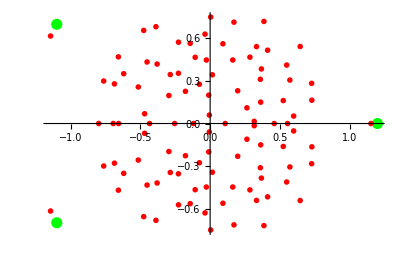

```mathematica
m=100;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={1.2,-1.1,0.7};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
EValPic=ListPlot[{ReIm[Eigenvalues[AExtra]],ReIm[Eigenvalues[A]]},
PlotRange->All,
PlotStyle->{{Green, PointSize[0.02]},{Red,PointSize[0.01]}},
AspectRatio->Automatic]
```

Lets see what the Arnoldi lemniscate pictures look like for this.

```mathematica
Clear[MaxIter,Q0,H0,HData,p,c,n,z]
MaxIter=20;
b=Normalize[RandomReal[{-1,1},m]];
{Q0,H0}={{b}ᵀ,{{}}};
HData=NestList[Arnoldi[A],{Q0,H0},MaxIter]⟦2;;MaxIter,2⟧;
TabView[Map[MatrixPlot,HData],MaxIter-1];
Clear[p,n]
TabView[
Table[
H=HData⟦n⟧;
p[n][z_]=CharacteristicPolynomial[H⟦1;;n⟧,z];
c[n]=Norm[p[n][A].b];
{p[n][z],c[n],H⟦-1,-1⟧},
{n,1, Length[HData]}],Length[HData]];
TabView[
Table[ 
Show[EValPic,
ContourPlot[Abs[p[n][x+I y]]==c[n],{x,-1.2,2.1},{y,-1.0,1.0},
PlotPoints->100],
Prolog->{LightPink, Disk[{0,0},1]},
Epilog->Point[ReIm[Eigenvalues[HData⟦n,1;;n⟧]]]],
{n, 1, Length[HData]}]
]
```

12345678910111213141516171819

You can see the blue curve bulge, then pinch of, and then shrink down on the “external” eigenvalue.  This is what Arnoldi does.  The question is can we use polynomials to understand the asymptotic convergence.

## Arnoldi is “Optimal”

The Arnoldi process produces the best monic (lead coefficient equals one) polynomial in the sense that 
	𝓅_n(z)=det(z I-(Ĥ)_n)=argmin_(p∈𝒫_n)||p(A).b||
 where 𝒫_n={z^n+c_(n-1)z^(n-1)+…+c_2 z^2+c_1 z+c_0}.  This looks weird but it is just orthogonality in the Arnoldi process and the Cayley-Hamilton (CH) theorem “Matrices satisfy their  own characteristic polynomial”.

p(A).b=A^n.b-Q_n.y for p∈𝒫_n and some y∈ℂ^n. So
	argmin_(p∈𝒫_n)||p(A).b|| | ⟺ | y_best=argmin_(y∈ℂ^n)||A^n.b-Q_n.y||.

The point in 𝒦_n(A,b) nearest A^n.b is simply y_best=(Q_n)†.A^n.b.

The minimum value is ||(I_m-Q_n.(Q_n)†).A^n.b||

Continuing Arnoldi would give the Hessenberg decomposition 
	A=Q_m.(Ĥ)_m.(Q_m)†

Q_m=[Q_n | | | Q_rest]  and (Ĥ)_m[1:n+1,1:n]=H_n

p(A)=P(Q_m.(Ĥ)_m.(Q_m)†)=Q_m.p((Ĥ)_m).(Q_m)†

So y_best=(Q_n)†.Q_m.((Ĥ)_m)^n.(Q_m)†.b tidies up (because 
(Q_n)†.Q_m=(I_n | | | 0_(n×m)) and (Q_m)†.b=(Q_m)†.q_1= e_1) to 
	y_best=(I_n|0_(n×m) ).((Ĥ)_m)^n.e_1=((Ĥ)_m)^n⟦1:n,:⟧.e_1=((Ĥ)_n)^n.e_1

In words, the optimal y is the first column of the nth power of (Ĥ)_n!

The characteristic polynomial gives ((Ĥ)_n)^n.

## Using Arnoldi “Optimality”

We know that any other polynomial gives a bigger value! for any monic polynomial p_n∈𝒫_n of the correct power
	||p_n(A).b||≥||𝓅_n(A).b||=c_n. 
This is surprisingly useful if we approximate 𝓅_n .If we are interested in the convergence to the large real eigenvalue λ≈1.3 after a while we can pick out the eigenvalue of (Ĥ)_n that is converging to λ. We have λ_n→λ and choose 
 	p_n(z)=z^(n-1)(z-λ_n)
 which is small on the unit disk (where all the other eigenvalues live) and zero at z=λ_n. It is a crude approximation to the characteristic polynomial.  Near z=λ_n we have 
 	|p_n(z)|~|λ_n|^(n-1)|z-λ_n|∼1.3^n|z-λ_n|
 which has one term that gets big.  If 
 	|p_n(λ)|∼Mc_n then 1.3^n|λ-λ_n|∼M c_n 
 and we would get the estimate
 	 |λ-λ_n|∼(1/1.3)^n M c_n 
which indicates geometric convergence. Lets see if we can see this happen.

```mathematica
m=400;
A=RandomReal[{-√(2/m),√(2/m)},{m,m}]; 
{i,j,k}={12,17,18};{γ,α,β}={1.3,0.2,0.3};
AExtra = ({{γ, 0, 0}, {0, α, β}, {0, -β, α}});A⟦{i,j,k},{i,j,k}⟧=AExtra;
λBig=Eigenvalues[A,1]⟦1⟧
```

1.26917+0. ⅈ

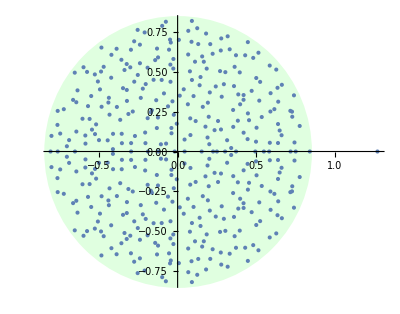

```mathematica
ListPlot[ ReIm[Eigenvalues[A]],AspectRatio->Automatic,
Prolog->{LightGreen, Disk[{0,0},0.85]}]
```

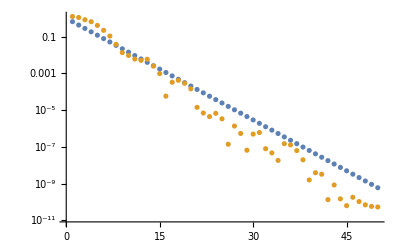

```mathematica
MaxIter=50;
b=Normalize[RandomReal[{-1,1},m]];
{Q,H}={{b}ᵀ,{{}}};
ListLogPlot[{
Table[(0.85/1.3)^n,{n,1, MaxIter}],
Table[
{Q,H}=Arnoldi[A][{Q,H}];
Abs[λBig-Eigenvalues[Drop[H,-1],1]⟦1⟧],
{MaxIter}]
}]
```

It does indeed converge geometrically i.e linearly.  The slope depends on the gap between the largest eigenvalue and the rest of the spectrum.  You need to be sneakier to understand the convergence to a complex conjugate pair.

## Bells and Whistles

### Block Arnoldi

On a GPU you can compute A.X with X∈ℝ^(m×16) in the same time as A.x with x∈ℝ^m.  For some details on the dominant GPU programming paradigm see the introduction in
	https://docs.nvidia.com/cuda/cuda-c-programming-guide/
Note, 16 is a small (but not completely atypical example) dimension for block algorithms that take advantage of such bulk buy efficiencies. I describe it as buy one get 15 free with even better discounts for larger blocks.  Not surprisingly, significantly larger block sizes are not common for large problems. 
	A block Arnoldi Process efficiently and incrementally generates a sequence of orthogonal basis Q_n and block Upper Hessenberg action matrix H_n with initial block B∈ℝ^(m×b) for the block Krylov Space 
	𝒦_n(A,B):=span({B,A.B,A^2.B,…,A^(n-1).B})
of dimension n*b.

### Filters and Restarts

As we saw Arnoldi naturally computes the “outside” eigenvalues.  If a linear solve is practical we can compute eigenvalues near a shift μ by building the shifted inverse Krylov space
	𝒦_n((A-μ I)^-1,B):=span({B,(A-μ I)^-1.B,…,(A-μ I)^-n.B}).
Repeated linear solves are rarely feasible and an alternative is to approximately filter needed eigenvectors from a standard Krylov space and repeatedly restart.  The standard restart consists of several steps of a Shifted QR algorithm to sweep the wanted algorithms to the bottom of the Hessenberg matrix.  The Krylov algorithm is then restarted with the bottom most Ritz vectors and the process is repeated.  This Implicitly Restarted Block Arnoldi is the standard algorithm for computing eigenvalues near any point on the outside border of the spectrum. Software provides access to various standard filters: largest positive real part, largest imaginary part, most negative real part, etc.

B=rand(m,b)
Until converged
	#Run n Block Arnoldi Steps
	(Q_n,(Ĥ)_n)←𝒦_n(A,B)
	#Extract Block Ritz Matrix
	H=(Ĥ)_n[1:n*b,1:n*b]
	#Filter H for eigen vectors near μ with q shifted QR steps
	do i in 1:q
		H-μ I=U.R; H=R.U+μ I
	end
	#Construct restarted Arnoldi Block from enriched subspace 
	B=Q_n.U[1:n*b,(n-1)*b:n*b]

Computing a few internal eigenvalues efficiently is a topic of active research.